-3.21851

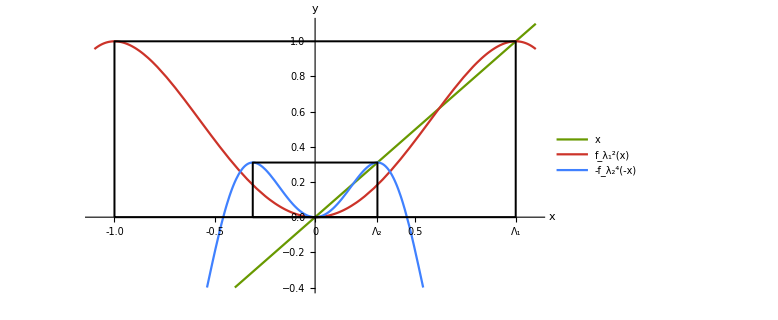

```mathematica
f[r_,x_]:=1-r*x^2;

(* the second superstable iterate of f *)
f2[x_]:=f[1,f[1,x]]; 

(* the fourth superstable iterate of f *)
f4[x_]:=Nest[f[1.31070264,#]&,x,4];
sol=y/.NSolve[f4[y]==y,y,Reals];

(* the current scaling factor *)
1/sol[[2]]

xticks=(Drop[Charting`FindTicks[{0,1},{0,1}]@@{-1,1},{5,5}])~Join~{{1 ,Subscript[Λ,1]},{Abs[sol[[2]]],Subscript[Λ,2]}};

Plot[{x,f2[x],-f4[x]},{x,-1.1,1.1},PlotRange->{{-1.1,1.1},{-0.4,1.1}},
Ticks->{xticks,Automatic},PlotStyle->ColorData[90],AspectRatio->1/1.8,
PlotLegends->Placed[{"x","f_λ_1^2(x)","-f_λ_2^4(-x)"},{0.9,0.11}],AxesLabel->{x,y},ImageSize->Large,Epilog->{EdgeForm[{Thickness[0.0025],Dashed,Black}],FaceForm[],Rectangle[{-1,0},{1,1}],Rectangle[{sol[[2]],f4[sol[[4]]]},{-sol[[2]],-f4[sol[[2]]]}]}]
```

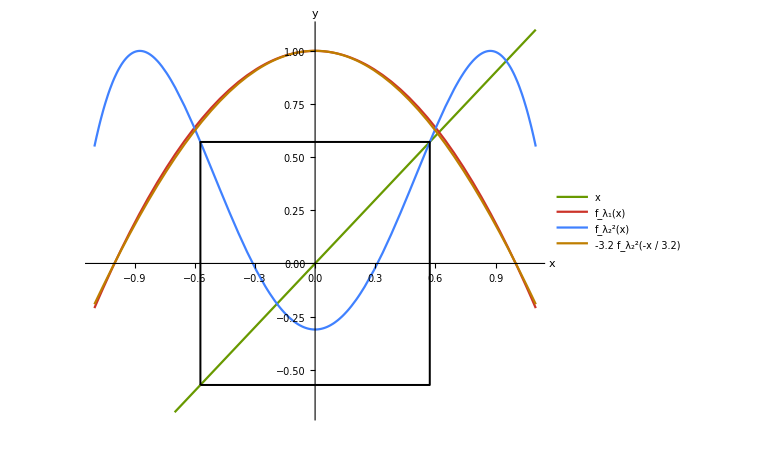

```mathematica
l2=1.31070264;
f[r_,x_]:=1-r*x^2;
f2[x_]:=f[l2,f[l2,x]];
f4[x_]:=Nest[f[l2,#]&,x,4];
sol=y/.NSolve[f2[y]==y,y,Reals];
sol2=y/.NSolve[f4[y]==y,y,Reals];

Plot[{x,f[1,x],f2[x],-3.22*f2[x/-3.22]},{x,-1.1,1.1},PlotRange->{{-1.1,1.1},{-0.7,1.1}},PlotStyle->ColorData[90],PlotLegends->Placed[{"x","f_λ_1(x)","f_λ_2^2(x)","-3.2 f_λ_2^2(-x / 3.2)"},{0.89,0.12}],AxesLabel->{x,y},ImageSize->Large,AspectRatio->0.8,Epilog->{EdgeForm[{Thickness[0.0025],Dashed,Black}],FaceForm[],Rectangle[{-sol[[3]],-f2[sol[[3]]]},{sol[[3]],f2[sol[[3]]]}]}]
```